```mathematica
numSteps = 25
AlternateSigns[x_] := If[Mod[x,2]==0, -x,x]
xdirections = Table[i, {i, numSteps}]                                            (* fill with 1,2,3,4,5... 25 *)
xdirections = Map[AlternateSigns,xdirections]                        (* alternate signs *)
xdirections = Riffle[xdirections,0]                                               (* mix in zeros *)
ydirections = Prepend[xdirections, 0]

coordinates = Table[{xdirections[[i]],ydirections[[i]]},{i,numSteps}]
coordinates2 = Table[{ydirections[[i+1]]+ydirections[[i]], xdirections[[i+1]]+ xdirections[[i]]},{i,numSteps}]
```

25

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

{1,-2,3,-4,5,-6,7,-8,9,-10,11,-12,13,-14,15,-16,17,-18,19,-20,21,-22,23,-24,25}

{1,0,-2,0,3,0,-4,0,5,0,-6,0,7,0,-8,0,9,0,-10,0,11,0,-12,0,13,0,-14,0,15,0,-16,0,17,0,-18,0,19,0,-20,0,21,0,-22,0,23,0,-24,0,25}

{0,1,0,-2,0,3,0,-4,0,5,0,-6,0,7,0,-8,0,9,0,-10,0,11,0,-12,0,13,0,-14,0,15,0,-16,0,17,0,-18,0,19,0,-20,0,21,0,-22,0,23,0,-24,0,25}

{{1,0},{0,1},{-2,0},{0,-2},{3,0},{0,3},{-4,0},{0,-4},{5,0},{0,5},{-6,0},{0,-6},{7,0},{0,7},{-8,0},{0,-8},{9,0},{0,9},{-10,0},{0,-10},{11,0},{0,11},{-12,0},{0,-12},{13,0}}

{{1,1},{1,-2},{-2,-2},{-2,3},{3,3},{3,-4},{-4,-4},{-4,5},{5,5},{5,-6},{-6,-6},{-6,7},{7,7},{7,-8},{-8,-8},{-8,9},{9,9},{9,-10},{-10,-10},{-10,11},{11,11},{11,-12},{-12,-12},{-12,13},{13,13}}

```mathematica
25
```

```mathematica
25
```

25

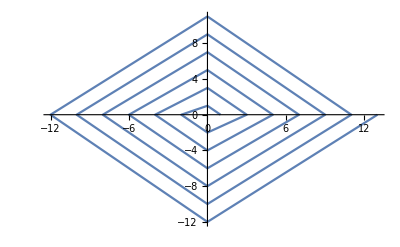

```mathematica
ListLinePlot[coordinates2]
```

```mathematica
Animate[
  ListLinePlot[coordinates2[[1;;i]],AspectRatio -> 1 , PlotRange->{{-15,15},{-15,15}}], {i, 1, numSteps, 1}
]
```